### Start choosing the example:

```mathematica
t=22;
beta = 1/2;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U1-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.006711,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→4.,u964→2.,u965→0,u966→4.,u967→-2+4.,u968→-2+2.,u969→0,u970→4.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→2.09306,u964→1.04653,u965→0,u966→0.+1. 2.09306,u967→0.+1. 1.04653,u968→0,u969→0,u970→0.+1. 2.09306|>

```mathematica
FFR
```

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→2.09306,u964→1.04653,u965→0,u966→0.+1. 2.09306,u967→0.+1. 1.04653,u968→0,u969→0,u970→0.+1. 2.09306|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→2.19814,u964→1.09907,u965→0,u966→0.+1. 2.19814,u967→0.+1. 1.09907,u968→0,u969→0,u970→0.+1. 2.19814|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→2.44322,u964→1.22161,u965→0,u966→0.+1. 2.44322,u967→0.+1. 1.22161,u968→0,u969→0,u970→0.+1. 2.44322|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→3.66698,u964→1.83349,u965→0,u966→0.+1. 3.66698,u967→0.+1. 1.83349,u968→0,u969→0,u970→0.+1. 3.66698|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 3.14018×10^-15

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→4.,u964→2.,u965→0,u966→0.+1. 4.,u967→0.+1. 2.,u968→0,u969→0,u970→0.+1. 4.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→4.88529,u964→2.44265,u965→0,u966→0.+1. 4.88529,u967→0.+1. 2.44265,u968→0,u969→0,u970→0.+1. 4.88529|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→7.28546,u964→3.64273,u965→0,u966→0.+1. 7.28546,u967→0.+1. 3.64273,u968→0,u969→0,u970→0.+1. 7.28546|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→8.69147,u964→4.34573,u965→0,u966→0.+1. 8.69147,u967→0.+1. 4.34573,u968→0,u969→0,u970→0.+1. 8.69147|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→8.69314,u964→4.34657,u965→0,u966→0.+1. 8.69314,u967→0.+1. 4.34657,u968→0,u969→0,u970→0.+1. 8.69314|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→32.7464,u964→16.3732,u965→0,u966→0.+1. 32.7464,u967→0.+1. 16.3732,u968→0,u969→0,u970→0.+1. 32.7464|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→8.77571,u964→4.38786,u965→0,u966→0.+1. 8.77571,u967→0.+1. 4.38786,u968→0,u969→0,u970→0.+1. 8.77571|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→8.86156,u964→4.43078,u965→0,u966→0.+1. 8.86156,u967→0.+1. 4.43078,u968→0,u969→0,u970→0.+1. 8.86156|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→9.03823,u964→4.51911,u965→0,u966→0.+1. 9.03823,u967→0.+1. 4.51911,u968→0,u969→0,u970→0.+1. 9.03823|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→9.61169,u964→4.80584,u965→0,u966→0.+1. 9.61169,u967→0.+1. 4.80584,u968→0,u969→0,u970→0.+1. 9.61169|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→10.7411,u964→5.37057,u965→0,u966→0.+1. 10.7411,u967→0.+1. 5.37057,u968→0,u969→0,u970→0.+1. 10.7411|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→13.9818,u964→6.99091,u965→0,u966→0.+1. 13.9818,u967→0.+1. 6.99091,u968→0,u969→0,u970→0.+1. 13.9818|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→19.7883,u964→9.89413,u965→0,u966→0.+1. 19.7883,u967→0.+1. 9.89413,u968→0,u969→0,u970→0.+1. 19.7883|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j949→2,j950→2,j951→2,j952→2,j953→0,j954→0,j955→0,j956→0,jt957→0,jt958→2,jt959→2,jt960→0,jt961→2,jt962→0,u963→32.7464,u964→16.3732,u965→0,u966→0.+1. 32.7464,u967→0.+1. 16.3732,u968→0,u969→0,u970→0.+1. 32.7464|>

### What we this plot for?

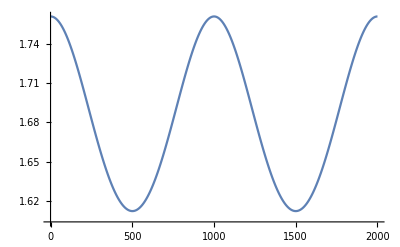

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.